# Atomic Nuclei

## Import Nist

```mathematica
nistCSDA=Flatten[{{{0.0003539,0.01},{0.0005192,0.0125},{0.0007111,0.015},{0.0009284,0.0175},{0.00117,0.02},{0.001724,0.025},{0.002367,0.03},{0.003094,0.035},{0.0039,0.04},{0.004783,0.045},{0.005738,0.05},{0.006763,0.055},{0.007855,0.06},{0.01023,0.07},{0.01284,0.08},{0.01568,0.09},{0.01872,0.1},{0.02714,0.125},{0.03659,0.15},{0.04693,0.175},{0.05804,0.2},{0.08217,0.25},{0.1083,0.3},{0.1361,0.35},{0.1652,0.4},{0.1952,0.45},{0.226,0.5},{0.2575,0.55},{0.2894,0.},{0.3545,0.7},{0.4206,0.8},{0.4874,0.9},{0.5546,1.},{0.7231,1.25},{0.8913,1.5},{1.058,1.75},{1.224,2.},{1.55,2.5},{1.869,3.},{2.183,3.5},{2.491,4.},{2.794,4.5},{3.092,5.},{3.386,5.5},{3.675,6.},{4.242,7.},{4.795,8.},{5.334,9.},{5.861,10.},{7.127,12.5},{8.328,15.},{9.472,17.5},{10.56,20.},{12.61,25.},{14.5,30.},{16.26,35.},{17.9,40.},{19.44,45.},{20.89,50.},{22.26,55.},{23.56,60.},{25.97,70.},{28.17,80.},{30.19,90.},{32.05,100.},{36.19,125.},{39.72,150.},{42.82,175.},{45.57,200.},{50.28,250.},{54.24,300.},{57.64,350.},{60.63,400.},{63.29,450.},{65.69,500.},{67.87,550.},{69.88,600.},{73.45,700.},{76.56,800.},{79.32,900.},{81.8,1000.}}},1];
```

```mathematica
placement=Below;
```

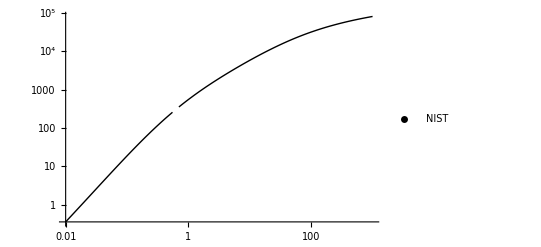

```mathematica
nistPlot=ListLogLogPlot[Transpose[{nistCSDA[[1;;,2]],1000 nistCSDA[[1;;,1]]}],PlotLegends->Placed[{"NIST"},placement],PlotRange->All,Joined->True,PlotStyle->Black]
```

## Accepted Plots

### Equations

```mathematica
RAccepted[Energy_]:=412 Energy^(1.265-0.0954 Log[ⅇ,Energy]) (* Energy in MeV,RAccepted in mg/cm^2*)
```

```mathematica
RAccepted2[Energy_]:=530 Energy-106(* Energy in MeV,RAccepted in mg *)
```

### Plots

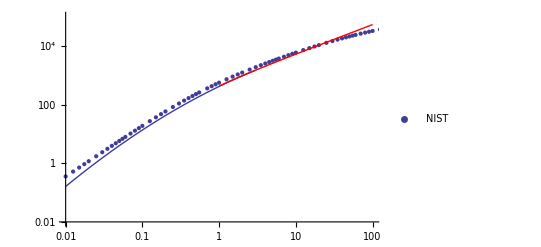

```mathematica
Show[LogLogPlot[RAccepted[Energylow],{Energylow,0.01,3},PlotRange->{{0.01,100},{0.01,100000}},PlotLegends->{"R(E) if E<3MeV"}],nistPlot,LogLogPlot[RAccepted2[Energy],{Energy,1,100},PlotRange->All,PlotStyle->Red,PlotLegends->{"R(E)if E>1MeV"}]]
```

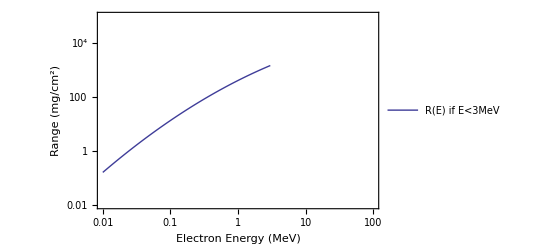

```mathematica
LogLogPlot[RAccepted[Energylow],{Energylow,0.01,3},PlotRange->{{0.01,100},{0.01,100000}},PlotLegends->{"R(E) if E<3MeV"} ,Frame->True,FrameLabel->{"Electron Energy (MeV)","Range (mg/cm^2)"},FrameStyle->{{FontSize->fontsize,FontFamily->fontfamily},{FontSize->fontsize,FontFamily->fontfamily}}]/.{fontfamily->"Times",fontsize->13}
```

### Calculations

```mathematica
peak1=RAccepted[0.624]/1000 (* Energy in MeV,RAccepted in g/cm^2 *)
```

0.222122

```mathematica
peak1/density/.density->2.70
```

0.0822673

## Aluminum

### Equations and Constants

```mathematica
ρAl=2.70; (* g/cm^3 *)
```

```mathematica
thicknessOfAl=3 18 10^-4 //N;(* cm *)
```

```mathematica
energies={624.259601577,601,577.5,550.5,505.5,470.5,450.5}/1000; (* in MeV *)
```

```mathematica
thicknesses = Table[x thicknessOfAl,{x,0,Length[energies]-1}];
```

```mathematica
data=Transpose[{energies,thicknesses}]; (* in MeV and cm *)
```

```mathematica
errorsAl={3,4,1.5,7.5,1.5,8.5,10.5}/1000; (*in MeV *)
```

```mathematica
Mean[errorsAl/energies 100]//N
```

1.0289

```mathematica
aluminumdistanceFunctionofEnergy=LinearModelFit[data,x,x,Weights->1/errorsAl^2];
```

```mathematica
maxEnergyDistance=aluminumdistanceFunctionofEnergy[0]
```

0.106876

0.106876

0.106876

«2 more identical outputs»

```mathematica
minEnergyDistance=maxEnergyDistance-6*thicknessOfAl
```

0.0744755

0.0744755

0.0744755

«2 more identical outputs»

```mathematica
RangeMine[Energy_]:=(maxEnergyDistance-aluminumdistanceFunctionofEnergy[Energy]) 1000 ρAl(* Energy is in MeV and R is in mg/cm^2 *)
```

```mathematica
Rvalues=Transpose[{energies,Map[RangeMine[#]&,energies]}]//N
```

{{0.62426,283.05},{0.601,272.504},{0.5775,261.848},{0.5505,249.606},{0.5055,229.202},{0.4705,213.333},{0.4505,204.264}}

```mathematica
parametersofFit=FindFit[Rvalues,k x^b,{k,b},x]
```

{k→453.417,b→1.}

{k→453.417,b→1.}

{k→453.417,b→1.}

```mathematica
parametersofFit2=FindFit[Rvalues,k x^(b-a Log[E,x]),{k,b,g,a},x]
```

{k→453.417,b→1.,g→1.,a→-4.32979×10^-15}

```mathematica
fitOfRvalues2[Energys_]:=k Energys^(b-a Log[E,Energys])/.parametersofFit2
```

```mathematica
fitOfRvalues2[0.6]
```

272.05

```mathematica
fitOfRvalues[Energys_]:=k Energys^b/.parametersofFit
```

```mathematica
errorOfdata=Map[ErrorBar[#,fitOfRvalues[#]]&,errorsAl]//N
```

{ErrorBar[0.003,1.36025],ErrorBar[0.004,1.81367],ErrorBar[0.0015,0.680126],ErrorBar[0.0075,3.40063],ErrorBar[0.0015,0.680126],ErrorBar[0.0085,3.85405],ErrorBar[0.0105,4.76088]}

```mathematica
dataForError=Map[{#,fitOfRvalues[#]}&,energies]
```

{{0.62426,283.05},{601/1000,272.504},{0.5775,261.848},{0.5505,249.606},{0.5055,229.202},{0.4705,213.333},{0.4505,204.264}}

```mathematica
errorDataReadyForPlot=Table[{dataForError[[i]],errorOfdata[[i]]},{i,1,Length[energies]}];
```

### Calculations

```mathematica
Needs["ErrorBarPlots`"]
```

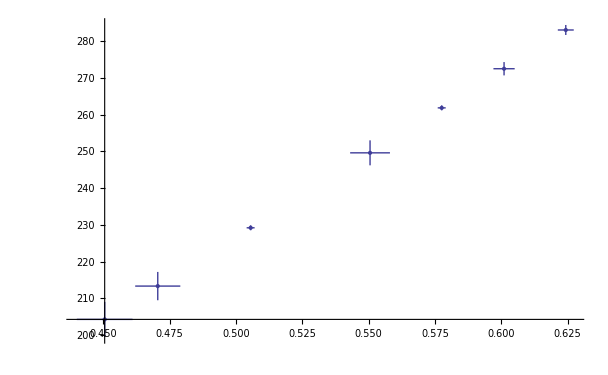

```mathematica
errorplot=ErrorListPlot[errorDataReadyForPlot,PlotRange->All,
ErrorBarFunction->Automatic]
```

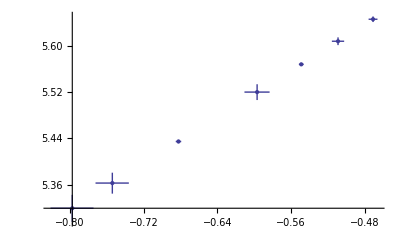

```mathematica
lerrorplot=errorplot/.{x_Real,y_Real}->{Log[E,x],Log[E,y]}
```

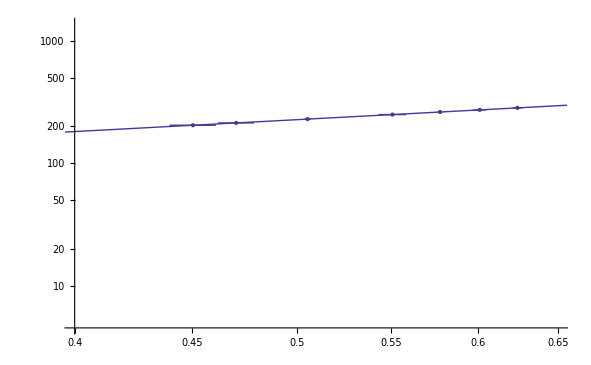

```mathematica
Show[LogLogPlot[fitOfRvalues[x],{x,0.01,3},PlotRange->{{.40,.65},Automatic}],lerrorplot]
```

### Plots

```mathematica
plotsAl1=LogLogPlot[{453.41580865214763 E0^0.9999981203747275},{E0,0.01,3},PlotRange->{{0.01,3},{0.01,100000}},PlotLegends->Placed[{"453.4 E"},placement],PlotStyle->{Green,FontSize->18,FontFamily->fontfamily},Frame->True,FrameLabel->{"Electron Energy (MeV)","Range (mg/cm^2)"},PlotLabel->"R(E) comparison",FrameStyle->{{FontSize->fontsize,FontFamily->fontfamily},{FontSize->fontsize,FontFamily->fontfamily}}]/.{fontfamily->"Times",fontsize->13};
```

```mathematica
plotsAl2=LogLogPlot[{412 E0^(1.265-0.0954 Log[E,E0])},{E0,0.01,3},PlotRange->{{0.01,3},{0.01,100000}},PlotLegends->Placed[{"412 E^(1.265 - 0.0954 ln (E))"},placement],Frame->True,FrameLabel->{"Electron Energy (MeV)","Range (mg/cm^2)"},PlotLabel->"R(E) comparison",FrameStyle->{{FontSize->fontsize,FontFamily->fontfamily},{FontSize->fontsize,FontFamily->fontfamily}}]/.{fontfamily->"Helvetica",fontsize->13};
```

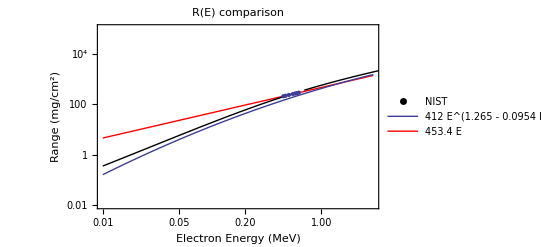

```mathematica
Show[plotsAl1,plotsAl2,nistPlot,lerrorplot]
```

### Plots2

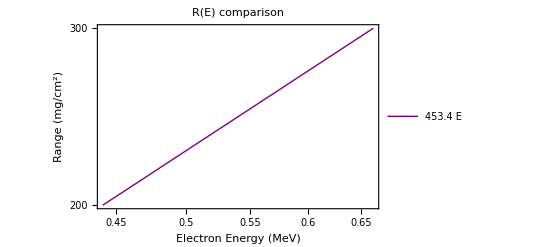

```mathematica
plotsAl11=LogLogPlot[fitOfRvalues[E0],{E0,0.4,65},PlotRange->{All,{200,300}},PlotLegends->Placed[{"453.4 E"},placement],PlotStyle->{Purple,FontSize->18,FontFamily->fontfamily},Frame->True,FrameLabel->{"Electron Energy (MeV)","Range (mg/cm^2)"},PlotLabel->"R(E) comparison",FrameStyle->{{FontSize->fontsize,FontFamily->fontfamily},{FontSize->fontsize,FontFamily->fontfamily}}]/.{fontfamily->"Times",fontsize->13}
```

```mathematica
plotsAl22=LogLogPlot[RAccepted[E0],{E0,0.01,3},PlotRange->{{0.01,3},{0.01,100000}},PlotLegends->Placed[{"412 E^(1.265 - 0.0954 ln (E))"},placement],Frame->True,FrameLabel->{"Electron Energy (MeV)","Range (mg/cm^2)"},PlotLabel->"R(E) comparison",FrameStyle->{{FontSize->fontsize,FontFamily->fontfamily},{FontSize->fontsize,FontFamily->fontfamily}}]/.{fontfamily->"Helvetica",fontsize->13};
```

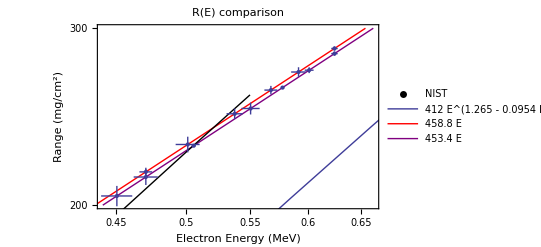

```mathematica
Show[plotsAl11,plotsPl11,plotsAl22,nistPlot,lerrorplotPl,lerrorplot]
```

## SavePlots

```mathematica
SetDirectory["/Users/kevin/SkyDrive/KTH Work/LaTeX Reports/Atomic Nucleus/Figures"];
```

```mathematica
(*Export["R_E_Comparison.eps",Show[plotsAl1,plotsAl2,nistPlot]]*)
```

R_E_Comparison.eps

```mathematica
Export["R_E_Error_ComparisonFullZoomIn.eps",Show[plotsAl11,plotsPl11,plotsAl22,nistPlot,lerrorplotPl,lerrorplot]]
```

R_E_Error_ComparisonFullZoomIn.eps

```mathematica
453.4 .003
```

1.3602

```mathematica
453.4 0.624
```

282.922

## Plastic

```mathematica
thicknessOfPlastic=0.01; (* cm *)
```

```mathematica
energiesOfPl={624.259,591.5,567.5,537.5,501,470.5,413};
```

```mathematica
thicknessesPl ={0.,0.01,0.02,0.03,0.04,0.05,0.07}
```

{0.,0.01,0.02,0.03,0.04,0.05,0.07}

```mathematica
dataPl={energiesOfPl,thicknessesPl};
```

```mathematica
Transpose[dataPl]//MatrixForm
```

(624.259 | 0.
591.5 | 0.01
567.5 | 0.02
537.5 | 0.03
501 | 0.04
470.5 | 0.05
413 | 0.07)

```mathematica
line=Fit[Transpose[dataPl], {1,x},x]
```

0.205466-0.000328793 x

```mathematica
EnergyAsFunctionOf[x_]:=0.20546613374720163-0.00032879292277015207 x
```

```mathematica
Solve[EnergyAsFunctionOf[0]==x,x] (* Gives Distance in cm to stop electron to zero in Plastic *)
```

{{x→0.205466}}

```mathematica
errorPl={3,6.5,5.5,6.5,9,4.5,13}
```

{3,6.5,5.5,6.5,9,4.5,13}

```mathematica
lm=LinearModelFit[Transpose[dataPl],x,x,Weights->1/errorPl^2]//Normal
```

0.204748-0.000327697 x

```mathematica
lm[{"BestFit","ParameterTable"}]
```

(0.204748-0.000327697 x)[{BestFit,ParameterTable}]

```mathematica
fitWithErrors[x_]:=0.2047476945240543-0.000327696558898258 x
```

```mathematica
Solve[fitWithErrors[0]==x,x]
```

{{x→0.204748}}

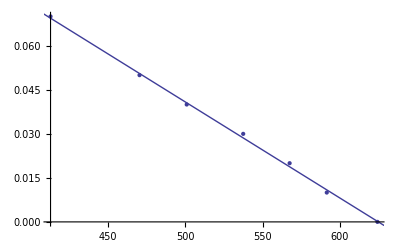

WolframAlphaQueryResults

```mathematica
Show[{ListPlot[Transpose[dataPl]],Plot[fitWithErrors[x],{x,0,700}]}]
```